```mathematica
Needs["Palicje`"];
vozlisca = {{0,0},{1,0},{3/2,Sqrt[3]/2},{1/2,Sqrt[3]/2}};
povezave = {{2,4},{1,3,4},{2,4},{1,2,3}};
podpore={{1,{Fpx[1],Fpy[1]}},{2,{0,Fpy[2]}}};
obremenitve = {{3,{0,-1}}};
```

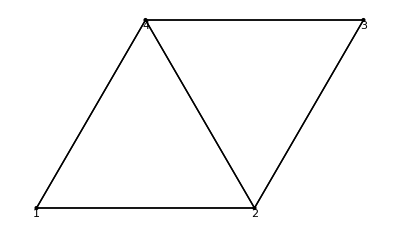

{{F[1,2]→-1/(2 √3),F[1,4]→1/(√3),F[2,3]→-2/(√3),F[2,4]→-1/(√3),F[3,4]→1/(√3)}}

{{F[1,2]→-1/(2 √3),F[1,4]→1/(√3),F[2,3]→-2/(√3),F[2,4]→-1/(√3),F[3,4]→1/(√3)}}

{{F[1.,2.]→-0.288675,F[1.,4.]→0.57735,F[2.,3.]→-1.1547,F[2.,4.]→-0.57735,F[3.,4.]→0.57735}}

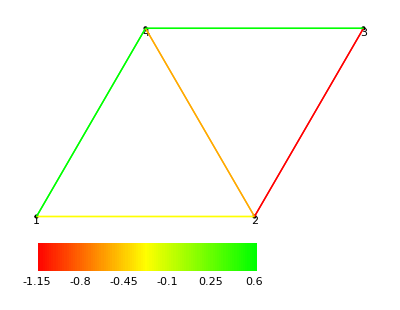

```mathematica
NarisiPalicje[vozlisca,povezave]
enacbe = GenerirajEnacbe[vozlisca, povezave, obremenitve, podpore];
neznanke = GenerirajNeznanke[povezave,podpore];
Solve[enacbe,neznanke]
resitev=ResiPalicje[vozlisca,povezave,podpore,obremenitve]
N[resitev]
NarisiBarvnoPalicje[vozlisca,povezave,resitev]
```

```mathematica
S=GenerirajS[povezave,1];
Y=GenerirajY[povezave,1];
energija=GenerirajEnergijsko[vozlisca,povezave,obremenitve,S,Y];
vezi = GenerirajVezi[podpore];
neznanke=GenerirajNeznankePomiki[vozlisca];
NMinimize[{energija,vezi},neznanke]
ResiPalicje[vozlisca,povezave,podpore,obremenitve,Y,S]
```

{-2.35706,{px[1]→0,py[1]→0,px[2]→-0.0330781,py[2]→0,px[3]→-0.587884,py[3]→-2.79464,px[4]→0.0371097,py[4]→-1.78639}}

{-2.35706,{px[1]→0,py[1]→0,px[2]→-0.0330781,py[2]→0,px[3]→-0.587884,py[3]→-2.79464,px[4]→0.0371097,py[4]→-1.78639}}

```mathematica
?Palicje`*
```

```mathematica
?F
??GenerirajEnacbe
```

Neznanka, uporabljena za notranje sile.

Vrne sistem ravnovesnih enačb za vsa vozlišča, upoštevajoč obremenitve, podpore in notranje sile

GenerirajEnacbe[Private`Vozlisca_,Private`Povezave_,Private`Obremenitve_,Private`Podpore_]:=Module[{Private`Sistem,Private`SileVozlisca},Private`SileVozlisca=Table[SileNaVozlisce[Private`i,Private`Vozlisca,Private`Povezave],{Private`i,1,Length[Private`Vozlisca]}];DodajObremenitve[Private`Obremenitve,Private`SileVozlisca];DodajObremenitve[Private`Podpore,Private`SileVozlisca];Flatten[Table[Thread[Private`SileVozlisca⟦Private`i⟧==0],{Private`i,Length[Private`Vozlisca]}]]]